```mathematica
SetDirectory["C:\\Users\\Emerson\\Documents\\___2024\\Alan"]
```

C:\Users\Emerson\Documents\___2024\Alan

## FA model

```mathematica
co=Import["em91CO.dat"];
fb=Import["em91FB.dat"];
fl=Import["em91FL.dat"];
oh=Import["em91OH.dat"];
ϕ=Import["em91FI.dat"];
```

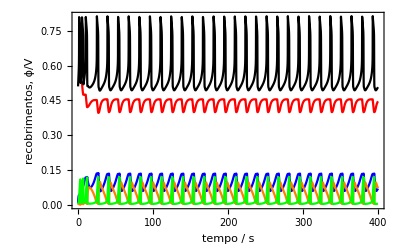

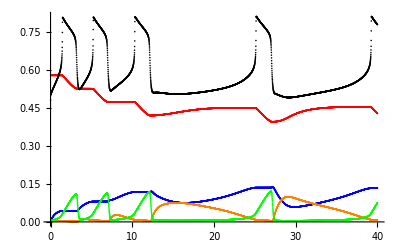

```mathematica
g=ListPlot[{co,fb,fl,oh,ϕ},PlotStyle->{Red,Blue,Orange,Green,Black},Joined->True,FrameLabel->{"tempo / s", "recobrimentos, ϕ/V"},Frame->True,RotateLabel->True]
```

```mathematica
Length[co]
```

4000

## example A + B --> C

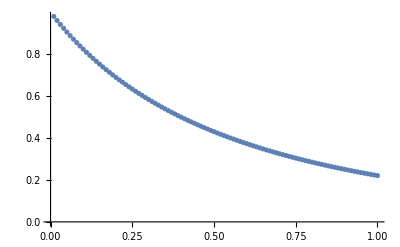

```mathematica
a=Import["a.dat"];
ListPlot[a,AxesOrigin->{0,0}]
```

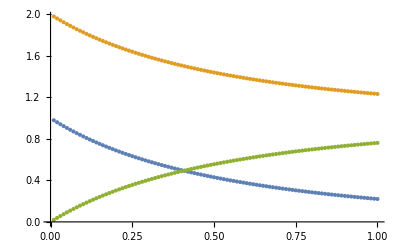

```mathematica
b=Import["b.dat"];
c=Import["c.dat"];
ListPlot[{a,b,c},AxesOrigin->{0,0}]
```

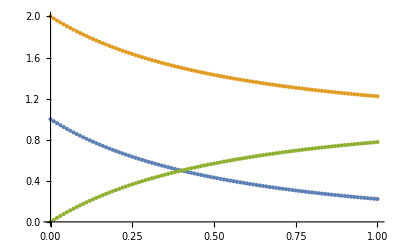

```mathematica
av=Import["av.dat"];
bv=Import["bv.dat"];
cv=Import["cv.dat"];
ListPlot[{av,bv,cv},AxesOrigin->{0,0}]
```